```mathematica
Table[0,{i,9},{j,9}]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[%5]
```

```mathematica
H=({{0, -1, 0, 0, 0, -1, -1, -1, 0}, {0, 0, -1, 0, 0, 0, -1, 0, -1}, {0, 0, 0, -1, 0, 0, 0, -1, -1}, {0, 0, 0, 0, -1, 0, -1, -1, 0}, {0, 0, 0, 0, 0, -1, -1, 0, -1}, {0, 0, 0, 0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
HH=H+Transpose[H];
```

```mathematica
MatrixForm[HH]
```

(0 | -1 | 0 | 0 | 0 | -1 | -1 | -1 | 0
-1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1
0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | -1
0 | 0 | -1 | 0 | -1 | 0 | -1 | -1 | 0
0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1
-1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1
-1 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0
-1 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
0 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 0)

```mathematica
Eigensystem[HH]
```

{{-4,2,2,2,2,-1,-1,-1,-1},{{1,1,1,1,1,1,1,1,1},{0,0,-1,1,-1,0,0,0,1},{-1,1,-1,0,0,0,0,1,0},{0,-1,1,-1,0,0,1,0,0},{-1,1,-1,1,-1,1,0,0,0},{-1,0,1,0,0,0,-1,0,1},{-1,-1,1,1,0,0,-1,1,0},{1,0,-1,-1,0,1,0,0,0},{-1,-1,0,1,1,0,0,0,0}}}

```mathematica
A={1,1,1,1,1,1,1-g,1-g,1-g};
```

```mathematica
EE=(A.HH.A)/A.A
```

(-24-12 (1-g)+12 g)/(6+3 (1-g)^2)

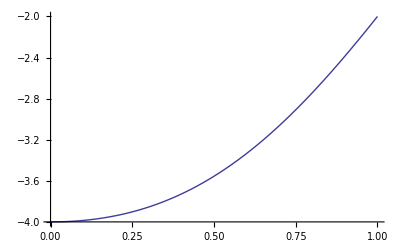

```mathematica
Plot[EE,{g,0.0,1.0}]
```